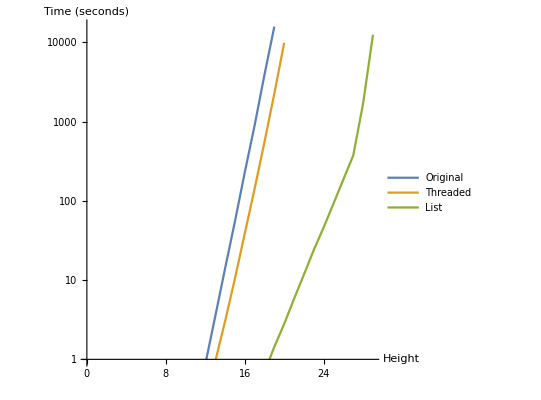

```mathematica
ClearAll["Global`*"]
old=Import[FileNameJoin[{NotebookDirectory[],"old_performance.csv"}]];
threaded=Import[FileNameJoin[{NotebookDirectory[],"threaded_performance.csv"}]];
new=Import[FileNameJoin[{NotebookDirectory[],"new_performance.csv"}]];
plot=ListLinePlot[{old,threaded,new},PlotLegends->{"Original","Threaded","List"},AspectRatio->1,AxesLabel->{"Height","Time (seconds)"},ScalingFunctions->"Log",PlotRange->{Automatic,{1,Automatic}}]

Export[FileNameJoin[{NotebookDirectory[],"performance.png"}],plot];
```